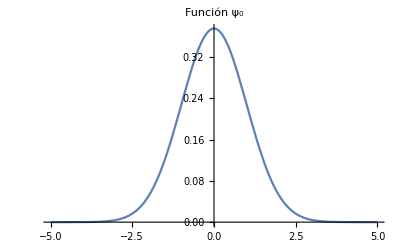

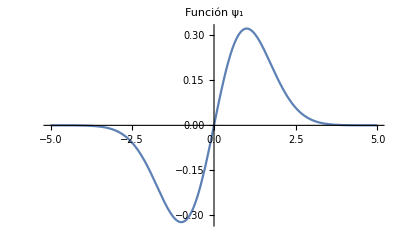

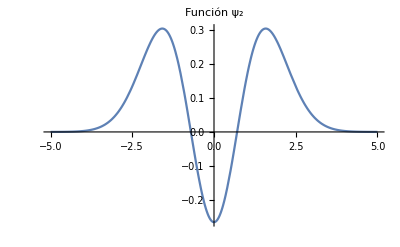

```mathematica
m=1;
ω=1;
ℏ=UnitConvert[Quantity[1,"PlanckConstant"],"SIBase"];
ℏ=QuantityMagnitude[ℏ];
ℏ=1;

ψ[z_,n_]:=1/2 1/Sqrt[2^n n!] ((m ω)/(π ℏ))^(1/4) Exp[-((m ω z^2)/(2 ℏ))] HermiteH[n,Sqrt[(m ω)/ℏ] z];
Plot[ψ[z, 0],{z,-5,5},PlotLabel->Style["Función ψ_0", FontSize->14, Black]]
Plot[ψ[z, 1],{z,-5,5},PlotLabel->Style["Función ψ_1", FontSize->14, Black]]
Plot[ψ[z, 2],{z,-5,5},PlotLabel->Style["Función ψ_2", FontSize->14, Black]]
```